```mathematica
Needs["Obtuse`"];
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

RadialBasisFunction::shdw: Symbol "RadialBasisFunction" appears in multiple contexts {"Obtuse`", "Global`"}; definitions in context "Obtuse`" may shadow or be shadowed by other definitions.

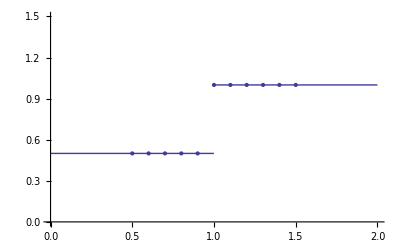

```mathematica
piece=Piecewise[{{0.5,x<1},{1,x≥1}}];
data=Table[{t,%/.x->t},{t,Range[0.5,1.5,0.1]}];
pieceplot=Plot[piece,{x,0,2}];
dataplot=ListPlot[data];
Show[pieceplot,dataplot, AxesOrigin->{0,0},PlotRange->{0,1.5}]
```

```mathematica
ϵ=1/(2r0^2);
```

```mathematica
1.0/0.0025
```

```mathematica
Sqrt[0.0025]/2
```

0.025

```mathematica
RBFPlot[r0_]:=Plot[Interpolation[data,Method->"RBF",RadialBasisFunction->((Exp[-#/(2 r0^2)])&)][x],{x,0.5,1.5}];
```

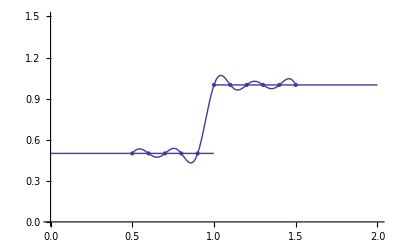

```mathematica
Show[{pieceplot,dataplot,RBFPlot[0.1]}, AxesOrigin->{0,0},PlotRange->{0,1.5}]
```